```mathematica
data=Flatten[Import["D:\\Doc\\tpu\\многомерные статистические методы\\data8.xlsx"],1];
```

```mathematica
n=Length[data]
```

100

```mathematica
X=Standardize[data]; k=10;
```

```mathematica
A=Covariance[X]; Sled=Tr[A];
```

```mathematica
l=Eigenvalues[A]
```

{4.08136,2.32404,1.50822,1.08869,0.516874,0.235415,0.127129,0.0608317,0.0426237,0.0148184}

```mathematica
Table[Sum[l[[i]]/Sled,{i,1,j}],{j,1,k}]
```

{0.408136,0.64054,0.791362,0.900231,0.951918,0.97546,0.988173,0.994256,0.998518,1.}

Можно сделать вывод, что 3 компонента объясняют практически 80 % дисперсии. Поэтому можно остановиться на факторной модели трёх главных компонент

```mathematica
m=3; lv=Eigenvectors[A];
```

```mathematica
B=Table[lv[[i]],{i,1,m}];
 F=X.Transpose[B];
```

```mathematica
TableForm[%]
```

1.79533 | -0.496521 | -0.780727
-0.041683 | -1.14274 | 1.46192
-1.26085 | 0.755423 | -3.79797
-1.76898 | -0.716023 | -1.19772
0.829549 | -0.421196 | -1.21693
-1.1807 | -0.484159 | -0.298558
0.580521 | -0.0674881 | -0.248973
0.724284 | -0.578535 | -0.0115287
0.298452 | 0.0998482 | -1.34029
-2.20478 | 0.958831 | 1.59704
-2.95387 | -1.18891 | 1.10711
2.13216 | 1.47523 | 1.05123
0.366938 | 1.40138 | -1.0521
1.42522 | -1.53517 | -0.593591
-0.42058 | -1.22178 | -1.15436
1.62427 | -0.505705 | 0.392841
2.09486 | -0.109489 | -0.822654
0.13513 | 0.671901 | -0.427519
1.48969 | -0.0509683 | -0.192918
0.717779 | 1.65392 | 0.669746
-4.07664 | -1.1644 | 0.324831
-0.524281 | -1.26618 | -0.753445
0.660112 | -0.90341 | 0.388763
-1.26318 | -0.921231 | 0.598692
-0.445525 | -0.0358599 | 0.0963745
0.648442 | 0.931659 | 1.09361
0.378988 | -0.785262 | -0.105184
0.403747 | -1.12288 | -0.978223
-1.00371 | -0.513954 | -0.779171
2.13514 | 0.405046 | -0.495901
1.60529 | -0.641687 | -0.799108
-8.77765 | 2.72503 | -4.0504
-1.80005 | -0.719686 | 0.743209
0.40565 | -0.693711 | -1.05221
1.16528 | 0.765411 | -1.55736
-0.889375 | -0.306924 | 0.684577
2.12074 | -0.71043 | -0.546511
-0.104235 | 1.48642 | 1.92413
1.894 | 6.50056 | 4.91338
1.32514 | 1.74564 | 0.995591
-1.02453 | 2.68775 | -1.72678
0.261929 | 0.175283 | 0.0249368
1.42664 | -0.827269 | 0.755188
-0.687469 | 3.19786 | -0.861305
-3.87156 | -0.473034 | -0.87276
1.22167 | 0.172866 | -0.607392
-1.24148 | 0.419134 | 0.745915
1.70974 | 0.216896 | -0.246233
-4.68619 | -0.877118 | 1.85728
-0.120625 | -0.408756 | 0.678898
-0.540207 | 0.0516898 | 1.76507
2.3854 | -0.213681 | -0.632401
-5.06998 | 1.37665 | -0.905067
1.6507 | 0.141307 | -0.498848
-3.00225 | -2.17338 | 1.23063
0.29717 | -0.0842499 | -0.84
-3.46822 | -2.39355 | 1.85924
-0.832368 | 1.69348 | 1.06828
1.46755 | 0.33612 | 0.0332184
1.66087 | 0.370387 | -1.22034
0.510797 | 0.634382 | -1.67791
-0.218951 | -1.83521 | 0.37063
-0.103891 | -1.25545 | 1.25463
-3.86876 | -2.081 | 1.84281
0.935646 | -0.405635 | 0.0357677
-0.0464766 | 5.79103 | 2.46985
0.780304 | -0.994553 | 0.263359
-0.864073 | 1.1837 | -1.39606
2.06725 | -0.322026 | -0.205135
1.61879 | 0.722312 | -0.571194
0.853816 | -1.04576 | 0.926767
1.98878 | -0.963876 | -0.179981
0.813923 | -0.546885 | -0.555315
-1.94312 | -1.96861 | 0.648011
0.552004 | 1.39789 | -1.63844
1.86801 | 2.2068 | 0.0488076
1.36095 | -0.852651 | -0.0802115
2.18939 | -1.20688 | -0.311273
2.52583 | 0.0558653 | -0.240043
-1.47631 | -2.05973 | 0.708268
-2.65988 | -1.71913 | 0.99782
-1.55771 | -1.3418 | 0.707792
2.40902 | -0.50273 | -0.0867842
-0.108969 | -0.728417 | -0.622347
1.33041 | 1.31947 | -0.913397
-1.72849 | -0.348472 | 2.65738
1.58335 | 0.464872 | -0.175194
-0.0920706 | -1.92117 | 1.08412
1.5641 | -0.760241 | -0.665319
-0.176458 | -1.32686 | 0.313179
1.51936 | -0.57803 | -0.668869
1.41998 | 0.834821 | -0.356727
0.801195 | -0.250106 | 0.832133
1.64054 | -1.89231 | 0.0363774
-1.90868 | -0.195747 | 1.22528
0.750394 | -1.29859 | 0.142196
-5.83393 | 4.82697 | -1.20609
2.21316 | 1.71536 | 1.14152
1.99212 | 0.0253558 | -0.20507
1.52125 | 0.562644 | -1.34856

Начну первый этап кластерного анализа, присвою каждому наблюдению свой номер

```mathematica
NCL=Range[1,n];
```

```mathematica
F0=MapThread[#1->#2&,{F,NCL}];
```

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
AC=Agglomerate[F0,Linkage->"Ward", DistanceFunction->EuclideanDistance];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

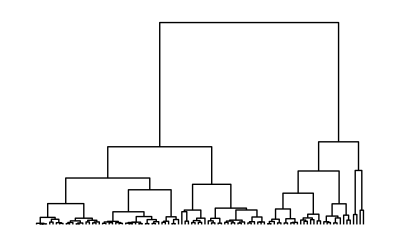

```mathematica
DendrogramPlot[AC]
```

Методом Варда определим последовательность разбиения наблюдений на кластеры.В качестве меры расстояния выберем евклидово расстояние, также построим дендрограмму кластеризации.
(**) =

```mathematica
Needs["ANOVA`"]
```

```mathematica
q = 11;
QQ = ClusterSplit[AC, q];
QQ1 = Table[If[IntegerQ[QQ[[i]]], {QQ[[i]]}, Sort[ClusterFlatten[QQ[[i]]]]], {i, 1, q}];
F1 = Flatten[Table[Map[{i, #} &, F[[All, 1]][[QQ1[[i]]]]], {i, 1, q}], 1];
F2 = Flatten[Table[Map[{i, #} &, F[[All, 2]][[QQ1[[i]]]]], {i, 1, q}], 1];
F3 = Flatten[Table[Map[{i, #} &, F[[All, 3]][[QQ1[[i]]]]], {i, 1, q}], 1];
An1 = ANOVA[F1, PostTests ->  Bonferroni, CellMeans -> False]
An2 = ANOVA[F2, PostTests ->  Bonferroni, CellMeans -> False]
An3 = ANOVA[F3, PostTests ->  Bonferroni, CellMeans -> False]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 10 | 361.503 | 36.1503 | 75.6109 | 4.16026×10^-39
Error | 89 | 42.5517 | 0.478109 |  | 
Total | 99 | 404.055 |  |  | ,PostTests→{Model→Bonferroni | {{1,5},{3,5},{4,5},{1,6},{2,6},{3,6},{4,6},{1,7},{2,7},{3,7},{4,7},{1,8},{2,8},{3,8},{4,8},{6,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{8,10},{9,10},{1,11},{2,11},{3,11},{4,11},{5,11},{6,11},{7,11},{8,11},{9,11},{10,11}}}}

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 10 | 193.397 | 19.3397 | 46.9214 | 3.3765×10^-31
Error | 89 | 36.6833 | 0.412171 |  | 
Total | 99 | 230.08 |  |  | ,PostTests→{Model→Bonferroni | {{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,6},{5,6},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{6,8},{7,8},{3,9},{4,9},{5,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{1,11},{2,11},{3,11},{4,11},{5,11},{6,11},{7,11},{8,11},{9,11},{10,11}}}}

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 10 | 111.559 | 11.1559 | 26.298 | 1.74622×10^-22
Error | 89 | 37.7548 | 0.424212 |  | 
Total | 99 | 149.314 |  |  | ,PostTests→{Model→Bonferroni | {{1,4},{3,4},{1,5},{2,5},{3,5},{4,5},{2,6},{4,6},{5,6},{1,7},{3,7},{5,7},{6,7},{1,8},{2,8},{3,8},{5,8},{6,8},{1,9},{3,9},{5,9},{6,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{1,11},{2,11},{3,11},{4,11},{6,11},{7,11},{8,11},{9,11},{10,11}}}}

```mathematica
q = 10;
QQ = ClusterSplit[AC, q];
QQ1 = Table[If[IntegerQ[QQ[[i]]], {QQ[[i]]}, Sort[ClusterFlatten[QQ[[i]]]]], {i, 1, q}];
F1 = Flatten[Table[Map[{i, #} &, F[[All, 1]][[QQ1[[i]]]]], {i, 1, q}], 1];
F2 = Flatten[Table[Map[{i, #} &, F[[All, 2]][[QQ1[[i]]]]], {i, 1, q}], 1];
F3 = Flatten[Table[Map[{i, #} &, F[[All, 3]][[QQ1[[i]]]]], {i, 1, q}], 1];
An1 = ANOVA[F1, PostTests ->  Bonferroni, CellMeans -> False]
An2 = ANOVA[F2, PostTests ->  Bonferroni, CellMeans -> False]
An3 = ANOVA[F3, PostTests ->  Bonferroni, CellMeans -> False]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 9 | 358.134 | 39.7927 | 77.9907 | 1.30515×10^-38
Error | 90 | 45.9202 | 0.510224 |  | 
Total | 99 | 404.055 |  |  | ,PostTests→{Model→Bonferroni | {{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{1,6},{2,6},{3,6},{1,7},{2,7},{3,7},{5,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10}}}}

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 9 | 193.182 | 21.4647 | 52.356 | 5.82849×10^-32
Error | 90 | 36.8978 | 0.409975 |  | 
Total | 99 | 230.08 |  |  | ,PostTests→{Model→Bonferroni | {{1,2},{1,3},{2,3},{1,4},{2,4},{3,5},{4,5},{2,6},{3,6},{4,6},{5,6},{1,7},{5,7},{6,7},{2,8},{3,8},{4,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10}}}}

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 9 | 108.208 | 12.0231 | 26.324 | 1.28499×10^-21
Error | 90 | 41.1062 | 0.456736 |  | 
Total | 99 | 149.314 |  |  | ,PostTests→{Model→Bonferroni | {{2,3},{1,4},{2,4},{3,4},{3,5},{4,5},{2,6},{4,6},{5,6},{1,7},{2,7},{4,7},{5,7},{2,8},{4,8},{5,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{5,10},{6,10},{7,10},{8,10},{9,10}}}}

Оптимальное количество разбиений = 10, так как при q=11 пропадает пара {1;2}. Поиск был произведён вручную при помощи команды “Ctrl+F”. Было произведено множественное сравнение средних по критерию Бонферрони.

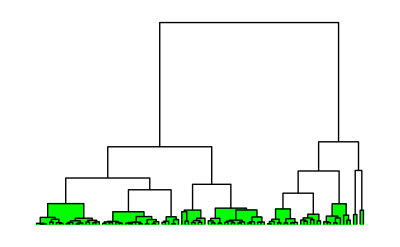

```mathematica
DendrogramPlot[AC,HighlightLevel->10]
```

```mathematica
QQ1
```

{{1,8,14,16,23,27,31,37,43,65,67,71,72,77,78,89,91,93,94,96},{17,19,30,46,48,52,54,59,60,69,70,79,83,85,87,92,99,100},{12,20,26,40,76,98},{3,13,35,41,44,61,68,75},{4,5,6,7,9,15,18,22,25,28,29,34,36,42,50,56,73,84},{2,24,33,62,63,74,80,82,88,90},{10,38,47,51,58,86,95},{11,21,45,49,53,55,57,64,81},{39,66},{32,97}}

```mathematica
q
```

10

Проведем разбиение объектов на 10 кластеров методом k - средних.

```mathematica
CL=FindClusters[F0,q,Method-> "KMeans", DistanceFunction->EuclideanDistance]
```

{{1,14,16,17,19,30,31,37,46,48,52,54,69,72,73,77,78,79,83,89,91,94,99},{2,7,8,23,27,42,43,50,62,63,65,67,71,88,90,93,96},{3,5,9,13,18,35,56,60,61,75,100},{4,6,15,22,25,28,29,34,84},{10,24,33,36,38,47,51,58,86,95},{11,21,45,49,55,57,64,74,80,81,82},{12,20,26,40,59,70,76,85,87,92,98},{32,53,97},{39,66},{41,44,68}}

```mathematica
F1 = Flatten[Table[Map[{i, #} &, F[[All, 1]][[CL[[i]]]]], {i, 1, q}], 1];
F2 = Flatten[Table[Map[{i, #} &, F[[All, 2]][[CL[[i]]]]], {i, 1, q}], 1];
F3 = Flatten[Table[Map[{i, #} &, F[[All, 3]][[CL[[i]]]]], {i, 1, q}], 1];
An1 = ANOVA[F1, PostTests ->  Bonferroni, CellMeans -> False]
An2 = ANOVA[F2, PostTests ->  Bonferroni, CellMeans -> False]
An3 = ANOVA[F3, PostTests ->  Bonferroni, CellMeans -> False]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 9 | 358.58 | 39.8422 | 78.8524 | 8.45353×10^-39
Error | 90 | 45.4748 | 0.505276 |  | 
Total | 99 | 404.055 |  |  | ,PostTests→{Model→Bonferroni | {{1,2},{1,3},{1,4},{1,5},{2,5},{3,5},{1,6},{2,6},{3,6},{4,6},{5,6},{2,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{5,9},{6,9},{8,9},{1,10},{6,10},{7,10},{8,10}}}}

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 9 | 189.917 | 21.1018 | 47.2862 | 2.49804×10^-30
Error | 90 | 40.1632 | 0.446258 |  | 
Total | 99 | 230.08 |  |  | ,PostTests→{Model→Bonferroni | {{1,3},{2,3},{3,4},{2,5},{1,6},{3,6},{5,6},{1,7},{2,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{9,10}}}}

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 9 | 108.904 | 12.1005 | 26.9497 | 6.08969×10^-22
Error | 90 | 40.4102 | 0.449002 |  | 
Total | 99 | 149.314 |  |  | ,PostTests→{Model→Bonferroni | {{1,2},{1,3},{2,3},{2,4},{1,5},{3,5},{4,5},{1,6},{3,6},{4,6},{3,7},{4,7},{5,7},{1,8},{2,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{2,10},{5,10},{6,10},{7,10},{9,10}}}}

```mathematica
FW=Table[F[[QQ1[[i]]]],{i,1,q}];
```

```mathematica
S=0;
For[i=1,i≤ 1,i++,ns=Length[QQ1[[i]]]; Ms=Mean[FW[[i]]]; For[j=1,j≤ ns, j++, S=S+(Norm[FW[[i,j]]-Mean[FW[[i]]]]^2)/ns; ]]
S
```

0.689113

Сумма квадратов до центров кластеров для метода Варда

```mathematica
FK=Table[F[[CL[[i]]]],{i,1,q}];
```

```mathematica
S=0;
For[i=1,i≤ 1,i++,ns=Length[CL[[i]]]; Ms=Mean[FK[[i]]]; For[j=1,j≤ ns, j++, S=S+(Norm[FK[[i,j]]-Mean[FK[[i]]]]^2)/ns; ]]
S
```

0.570528

Сумма квадратов до центров кластеров для метода k-средних. Можно сделать вывод, что встроенные функции в пакете(метод k-средних) более эффективнее.